CreateDirectory::filex: "C:\\Users\\Petr\\Desktop\\Projects\\Programming Techniques\\shown results\\collision\\" already exists.

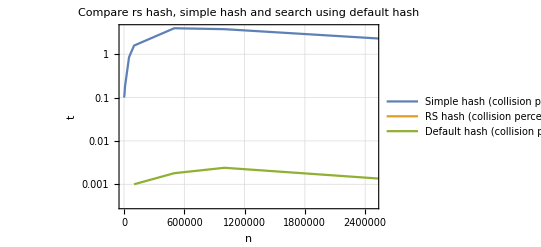

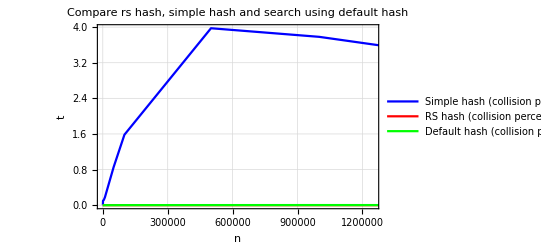

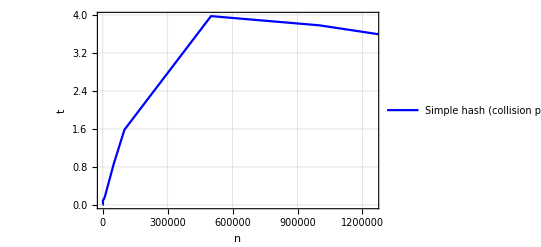

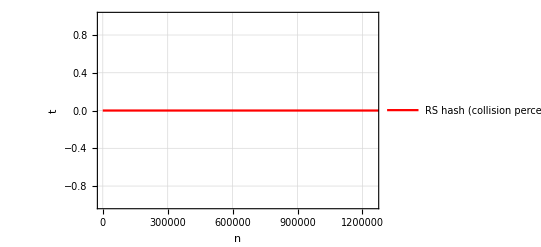

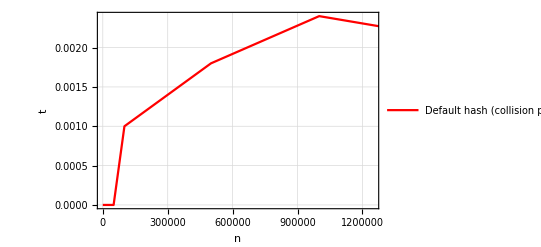

```mathematica
SetDirectory[NotebookDirectory[]];
workingDirectory = "../shown results";
SetDirectory[workingDirectory];
file= OpenRead["../logs/log_collision.txt"];
workingDirectory = CreateDirectory["collision"];
SetDirectory[workingDirectory];
filelist= ReadList[file,String];

defaultSearchResults = filelist[[3;;;;4]];
rsSearchResults = filelist[[2;;;;4]];
simpleSearchResults = filelist[[1;;;;4]];
simpleSearchResults= Map[({StringSplit[#][[5]],StringSplit[#][[8]]})&,simpleSearchResults];
rsSearchResults= Map[({StringSplit[#][[5]],StringSplit[#][[8]]})&,rsSearchResults];
defaultSearchResults= Map[({StringSplit[#][[5]],StringSplit[#][[8]]})&,defaultSearchResults];
simpleSearchResults= Map[({Read[StringToStream[#[[1]]],Number],N[100*Read[StringToStream[#[[2]]],Number]/Read[StringToStream[#[[1]]],Number]]})&,simpleSearchResults];
rsSearchResults= Map[({Read[StringToStream[#[[1]]],Number],N[100*Read[StringToStream[#[[2]]],Number]/Read[StringToStream[#[[1]]],Number]]})&,rsSearchResults];
defaultSearchResults= Map[({Read[StringToStream[#[[1]]],Number],N[100*Read[StringToStream[#[[2]]],Number]/Read[StringToStream[#[[1]]],Number]]})&,defaultSearchResults];
Plot1 = ListLogPlot[{simpleSearchResults, rsSearchResults, defaultSearchResults},Joined->True,PlotLegends->{"Simple hash (collision percentage)","RS hash (collision percentage)(no collisions)","Default hash (collision percentage)"},PlotLabel->"Compare rs hash, simple hash and search using default hash", AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]]
Plot2 = Show[ListPlot[simpleSearchResults,Joined->True,PlotStyle->Blue,PlotLegends->{"Simple hash (collision percentage)"},PlotLabel->"Compare rs hash, simple hash and search using default hash", AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]],ListPlot[rsSearchResults,Joined->True,PlotStyle->Red,PlotLegends->{"RS hash (collision percentage)"}],
ListPlot[defaultSearchResults,Joined->True,PlotStyle->Green,PlotLegends->{"Default hash (collision percentage)"}]]
Plot3 = ListPlot[simpleSearchResults,Joined->True,PlotStyle->Blue,PlotLegends->{"Simple hash (collision percentage)"}, AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]]
Plot4 = ListPlot[rsSearchResults,Joined->True,PlotStyle->Red,PlotLegends->{"RS hash (collision percentage)"}, AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]]
Plot5 = ListPlot[defaultSearchResults,Joined->True,PlotStyle->Red,PlotLegends->{"Default hash (collision percentage)"},AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]]
```

```mathematica
Export["Comp1.gif",Plot1,ImageSize->2048];
Export["Comp2.gif",Plot2,ImageSize->2048];
Export["Simple.gif",Plot3,ImageSize->2048];
Export["RS.gif",Plot4,ImageSize->2048];
Export["Default.gif",Plot5,ImageSize->2048];
```

```mathematica
grid = Grid[Transpose[{Join[{"Number"},rsSearchResults[[All,1]]],Join[{"Simple hash (collisons %)"},simpleSearchResults[[All,2]]],Join[{"RS hash (collisons %)"},rsSearchResults[[All,2]]],Join[{"Default hash (collisons %)"},defaultSearchResults[[All,2]]]}],Frame->All,Alignment->Left,Background->{None,{Yellow}},ItemStyle->Directive[FontSize->20,Bold]]
```

Number | Simple hash (collisons %) | RS hash (collisons %) | Default hash (collisons %)
5 | 0. | 0. | 0.
10 | 0. | 0. | 0.
50 | 0. | 0. | 0.
100 | 0. | 0. | 0.
500 | 0. | 0. | 0.
1000 | 0.1 | 0. | 0.
5000 | 0.12 | 0. | 0.
10000 | 0.18 | 0. | 0.
50000 | 0.854 | 0. | 0.
100000 | 1.583 | 0. | 0.001
500000 | 3.9748 | 0. | 0.0018
1000000 | 3.7815 | 0. | 0.0024
5000000 | 1.03822 | 0. | 0.00054

```mathematica
Export["TableHash.gif",grid,ImageSize->{2048,720}];
Export["TableHash.xls",grid,ImageSize->{2048,720}];
```